测试与条件

2+2 等于 4 吗？让我们来问问 Wolfram 语言。

测试 2+2 是否等于 4：

```mathematica
2+2==4
```

True

毫不奇怪，测试 2+2 是否等于 4 的结果是 True。

我们也可以测试 2×2 是否大于 5，我们使用 >。

测试 2×2 是否大于 5：

```mathematica
2*2>5
```

False

函数 If 让你在测试结果为 True 时给出一个结果，在测试结果为 False 时给出另一个结果。

由于测试的结果是 True，所以 If 的结果为 x：

```mathematica
If[2+2==4,x,y]
```

x

通过使用带 /@ 的纯函数，我们可以对一个列表中的每个元素应用 If。

如果一个元素小于 4，就把它设为 x，否则就设为 y：

```mathematica
If[#<4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,y,y,y}

你也可以用 ≤ 来测试小于等于，它可以使用 <= 来输入。

如果一个元素小于或等于 4，就把它设为 x；否则就把它设为 y：

```mathematica
If[#≤ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,x,y,y,y}

这将变成只有当一个元素等于 4 时，才会设为 x：

```mathematica
If[#== 4,x,y]&/@{1,2,3,4,5,6,7}
```

{y,y,y,x,y,y,y}

你可以使用 ≠ 来测试两个对象是否不相等，它可以使用 != 来输入。

如果一个元素不等于4，就把它设为 x；否则就把它设为 y：

```mathematica
If[#≠ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,x,x,x}

在一个列表中选出满足某个测试条件的元素往往很有用。你可以使用 Select 来完成此功能，并将你的测试作为一个纯函数。

选择列表中大于 3 的元素：

```mathematica
Select[{1,2,3,4,5,6,7},#>3&]
```

{4,5,6,7}

选择在 2 到 5 之间的元素：

```mathematica
Select[{1,2,3,4,5,6,7},2≤#≤5&]
```

{2,3,4,5}

除了像 <、> 以及 == 这样的大小比较，Wolfram 语言还包括许多其他类型的测试。例如 EvenQ 和 OddQ，它们测试数字是偶数还是奇数。(“Q”表示这些函数是在问一个问题)。

4 是一个偶数：

```mathematica
EvenQ[4]
```

True

从列表中选择偶数：

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ[#]&]
```

{2,4,6,8}

在本例中，我们不需要明确写出纯函数：

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ]
```

{2,4,6,8}

IntegerQ 用于测试对象是否为整数；PrimeQ 用于测试某数是否为质数。

选择质数：

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},PrimeQ]
```

{2,3,5,7}

有时我们需要进行组合测试。 && 表示”与”，|| 表示”或”，! 表示”非”。

选择列表中既是偶数又大于 2 的元素：

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]&&#>2&]
```

{4,6}

选择偶数或大于 4 的元素：

```mathematica
Select[{1,2,3,4,5,6,7},EvenQ[#]||#>4&]
```

{2,4,5,6,7}

选择既不是偶数也不大于 4 的元素：

```mathematica
Select[{1,2,3,4,5,6,7},!(EvenQ[#]||#>4)&]
```

{1,3}

还有许多其他的“Q 函数”可以用来问各种问题。LetterQ 用于测试一个字符串是否由字母组成。

字母之间的空格不是一个字母；“!”也不是：

```mathematica
{LetterQ["a"],LetterQ["bc"],LetterQ["a b"],LetterQ["!"]}
```

{True,True,False,False}

将一个字符串转换为一个字符列表，然后测试哪些是字母：

```mathematica
LetterQ/@Characters["30 is the best!"]
```

{False,False,False,True,True,False,True,True,True,False,True,True,True,True,False}

选择是字母的字符：

```mathematica
Select[Characters["30 is the best!"],LetterQ]
```

{i,s,t,h,e,b,e,s,t}

选择字母表中第 10 位之后的字母：

```mathematica
Select[Characters["30 is the best!"],LetterQ[#]&&LetterNumber[#]>10&]
```

{s,t,s,t}

你可以用 Select 来寻找英语中的回文词，也就是如果你把它们倒过来，它们还是一样的。

```mathematica
Select[WordList[ ],StringReverse[#]==#&]
```

{a,aha,bib,bob,boob,civic,dad,deed,dud,ere,eve,ewe,eye,gag,gig,huh,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,refer,rotor,sis,tat,tenet,toot,tot,tut,wow}

MemberQ 用于测试某个对象是否作为一个元素或成员出现在列表中。

5 出现在列表 {1,3,5,7} 中：

```mathematica
MemberQ[{1,3,5,7},5]
```

True

在 1 到 100 的范围内选择数字位数中包含 2 的数字：

```mathematica
Select[Range[100],MemberQ[IntegerDigits[#],2]&]
```

{2,12,20,21,22,23,24,25,26,27,28,29,32,42,52,62,72,82,92}

ImageInstanceQ 是一个基于机器学习的函数，用来测试一张图片是否是某一类事物的实例，比如一只猫。

测试一个图像是否是猫的图像：

```mathematica
ImageInstanceQ[-Graphics-,LinguisticAssistant]
```

True

选择猫的图像：

```mathematica
Select[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageInstanceQ[#,LinguisticAssistant]&]
```

{-Graphics-,-Graphics-}

这里有一个地理方面的 Select 的例子：在一个列表中找到哪些城市距离旧金山不到 3000 英里。

选择与旧金山的距离小于 3000 英里的城市：

```mathematica
Select[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoDistance[#,LinguisticAssistant]<LinguisticAssistant&]
```

{New York City,Chicago}

词汇

a==b |   | 测试是否相等
a<b |   | 测试是否小于
a>b |   | 测试是否大于
a≤b |   | 测试是否小于或等于
a≥b |   | 测试是否大于或等于
If[test,u,v] |   | 如果 test 为 True 将给出 u，如果为 False 则给出 v
Select[list,f] |   | 选择通过测试的元素
EvenQ[x] |   | 测试是否为偶数
OddQ[x] |   | 测试是否为奇数
IntegerQ[x] |   | 测试是否为整数
PrimeQ[x] |   | 测试是否为素数
LetterQ[string] |   | 测试是否仅包含字母
MemberQ[list,x] |   | 测试 x 是不是列表中的成员
ImageInstanceQ[image,category] |   | 测试图片是否为某一类别的实例

"共有 13 道习题"
"以及 7 道附加题" | "开始练习 »"

测试 123^321 是否大于 456^123。»

| 期望输出： |  
  | True |

计算 100 以内的数字中各位数之和小于 5 的数字。»

| 期望输出： |  
  | {1,2,3,4,10,11,12,13,20,21,22,30,31,40,100} |

把前 20 个整数列出来，其中质数用红色字体表示。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20} |

在 WordList[ ] 中找到以字母 “p” 开头和结尾的单词。»

| 期望输出： |  
  | {"pap","paperclip","parsnip","partisanship","partnership","pawnshop","payslip","peep","penmanship","pep","pickup","pileup","pimp","pip","plop","plump","polyp","pomp","poop","pop","premiership","prep","primp","professorship","prop","proprietorship","pulp","pump","pup"} |

列出前 100 个质数，只保留最后一位数字小于 3 的质数。»

| 期望输出： |  
  | {2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541} |

找到 100 以内的罗马数字中不包含 “I” 的那些。»

| 期望输出： |  
  | {"V","X","XV","XX","XXV","XXX","XXXV","XL","XLV","L","LV","LX","LXV","LXX","LXXV","LXXX","LXXXV","XC","XCV","C"} |

计算一个 1000 以内的罗马数字的列表，找出其中的回文字。»

| 期望输出： |  
  | {"I","II","III","V","X","XIX","XX","XXX","L","C","CXC","CC","CCC","D","M"} |

找到以相同字母开头和结尾的 100 以内的整数名称。»

| 期望输出： |  
  | {"nineteen","twenty-eight","thirty-eight","eighty-one","eighty-three","eighty-five","eighty-nine","ninety-seven"} |

从维基百科上关于 “words” 的文章中获取超过 15 个字符的单词的列表。»

| 期望输出示例： |  
  | {"orthographically","multiple-morpheme","Proto-Indo-European"} |

从 1000 开始，如果是偶数就除以 2，如果是奇数就计算 3#+1&；反复计算 200 次(科拉茨猜想)。»

| 期望输出： |  
  | {1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2} |

将维基百科上关于计算机的文章中的 5 个字母的单词创建为词云。»

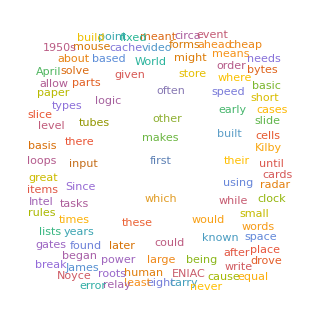
| 期望输出示例： |  
  | -Graphics- |

在 WordList[ ] 中找出前 3 个字母与后 3 个字母倒着读相同，但整个字符串不是回文的单词。»

| 期望输出： |  
  | {"despised","detected","detested","drainboard","foolproof","lackadaisical","marjoram","revolver"} |

在 WordList[ ] 中找到所有 10 个字母的单词，并且单词的 LetterNumber 值的总和为 100。»

| 期望输出： |  
  | {"accumulate","alienation","answerable","apoplectic","aquamarine","bewitching","censurable","ceramicist","chastening","chimpanzee","clementine","clinically","collecting","condensate","congenital","conjugated","connivance","declension","deliquesce","demobilize","demodulate","denominate","diagonally","discipline","discommode","egoistical","emasculate","embodiment","emendation","empathetic","fatalistic","fatherhood","geographer","hemoglobin","impugnable","inadequacy","interbreed","leveraging","liberalism","likelihood","martingale","mercantile","meridional","neoclassic","paramecium","plebiscite","potbellied","quadrangle","reciprocal","regimented","reschedule","researcher","scoreboard","septicemia","shibboleth","sleepyhead","stagecraft","stalemated","temperance","thickening","threatened","uncombined","unmodified"} |

创建一个 25 以内的整数表，将每一个以 3 结尾的整数都替换为 0。»

| 期望输出： |  
  | {1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25} |

使用 Table 和 If 来创建一个 5×5 的数组，其主对角线上为 1，其余为 0。»

| 期望输出： |  
  | {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} |

得到 1000 以内的数字列表，并且数字对 7 和 8 的模余都等于 1。»

| 期望输出： |  
  | {1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953} |

创建一个 100 以内的数字列表，其中 3 的倍数用黑色代替，5 的倍数用白色代替，3 和 5 的倍数用红色代替。»

| 期望输出： |  
  | {1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]} |

使用 Select 来获得质量大于地球的行星的列表。»

| 期望输出： |  
  | {"Jupiter","Saturn","Uranus","Neptune"} |

创建一个 50×50 的数组图示，如果 Mod[i,j]==0，则在位置 i,j 为黑色方块。»

| 期望输出： |  
  | -Graphics- |

创建一个 100×100 的数组图，如果一个方块的 x 和 y 位置的值都不包含 5，那么该位置为黑色方块。»

| 期望输出： |  
  | -Graphics- |

问&答

为什么要用 == 而不是 = 来测试相等？

因为 = 在 Wolfram 语言中表示其他的意思。如果你错误地使用 = 而不是 ==，你会得到非常奇怪的结果。(= 是用来给变量赋值的。)为了避免可能的混淆，== 通常读作“双等号”。

为什么“与”要写成 &&，而不是 &？

因为 & 在 Wolfram 语言中表示其他的意思。例如，它表示一个纯函数的结束。

==、>、&& 等是如何解释的？

== 为 Equal，≠ (!=) 为 Unequal，> 为 Greater，≥ 为 GreaterEqual，< 为 Less，&& 为 And，|| 为 Or，! 为 Not。

我在使用 &&、|| 等符号时什么时候需要使用括号？

这里也有类似于算术运算的运算顺序。&& 与 × 类似，|| 与 + 类似，而 ! 与 − 类似。所以 !p&&q 意思是“(非 p) 与 q”；而 !(p&&q) 的意思是“非(p 与 q)”。

Q 函数有什么特别之处？

他们是问一个问题，通常有一个 True 或 False 的答案。

还有哪些其他的 Q 函数？

NumberQ、StringContainsQ、BusinessDayQ 以及 ConnectedGraphQ。

除了使用 Select，是否有更好的方法来寻找具有某些属性的现实世界实体？

是的。你可以使用像 Entity["Country","Population"→GreaterThan[10^7 "people"]] 这样的函数来寻找“隐性实体”，然后使用 EntityList 来获得显性实体的列表。

技术笔记

在计算机科学中，True 和 False 通常被称为布尔值，这是根据 19 世纪中期乔治-布尔的名字命名的。带有 &&、|| 等符号的表达式通常被称为布尔表达式。

在 Wolfram 语言中，True 和 False 是符号，而不是像许多其他计算机语言那样用 1 和 0 来表示。

If 通常被称为条件。在 If[test,then,else] 中，除非 test 说他们的条件被满足，否则不会计算 then 和 else。

PalindromeQ 可以直接测试一个字符串是否是一个回文。

在 Wolfram 语言中，x 是一个符号(详见第 33 节)，可以代表任何东西，所以 x==1 只是一个等式，并不立即是 True 或 False。x===1(“三个等号”)测试 x 是否与 1 完全相等，由于它不相同，所以给出了 False。

探索更多

Wolfram 语言中的表达式测试指南 »

Wolfram 语言中的布尔运算指南 »